```mathematica
SetDirectory["/Users/calebhill/Documents/UNH/Research/code/github/graph_18b"];
q=Exp[2*Pi*I/42]; 
InDeg[z_]:=Module[{},Return[360 (z//Arg)/(2 Pi)]];
numericalPg = Import["./data/numerical_Pg.m"];
```

```mathematica
QIntsArr = Import["./data/q_ints_arr.m"];
NQIntsArr = Import["./data/n_q_ints_arr.m"];
```

Begin 6/7 work.

```mathematica
numericalPg[[1;;9]]//TableForm
```

0.333333
-0.166667-0.288675 ⅈ
-0.166667+0.288675 ⅈ
-0.166667+0.288675 ⅈ
0.333333
-0.166667-0.288675 ⅈ
-0.166667-0.288675 ⅈ
-0.166667+0.288675 ⅈ
0.333333

```mathematica
360 (-0.16666666666670188-0.28867513459483435 ⅈ//Arg)/(2 Pi)
 (-0.16666666666670188-0.28867513459483435 ⅈ//Abs)
```

-120.

0.333333

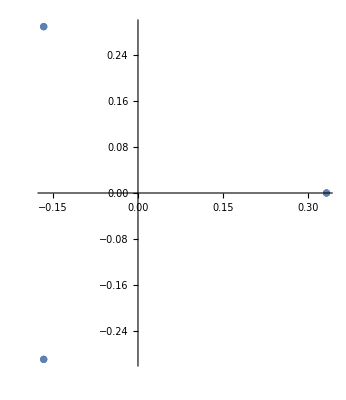

```mathematica
numericalPg[[1;;9]]//ComplexListPlot
```

```mathematica
numericalPg[[78;;93]]//Abs//TableForm
```

0.208712
0.234628
0.234628
0.234628
0.234628
0.263763
0.263763
0.263763
0.234628
0.263763
0.263763
0.263763
0.234628
0.263763
0.263763
0.263763

```mathematica
{Map[
InDeg, numericalPg[[78;;93]]
],
Map[
Abs, numericalPg[[78;;93]]
]}//Transpose//MatrixForm
```

(0 | 0.208712
-50.3494 | 0.234628
40.6987 | 0.234628
-170.349 | 0.234628
50.3494 | 0.234628
0 | 0.263763
91.0481 | 0.263763
-120. | 0.263763
-40.6987 | 0.234628
-91.0481 | 0.263763
0 | 0.263763
148.952 | 0.263763
170.349 | 0.234628
120. | 0.263763
-148.952 | 0.263763
0 | 0.263763)

```mathematica
0.2087121525221504/0.23462835144947158
```

0.889544

```mathematica
0.23462835144947158/0.26376261582589766
```

0.889544

```mathematica
1/0.8895436175244152
```

1.12417

```mathematica
0.8895436175244152//RootApproximant
```

Root0.890Root[-3+3 #1^2+#1^4&,2]0.8895436175241325

```mathematica
1/Root"0.890"Root[-3+3 #1^2+#1^4&,2]0.8895436175241325//RootApproximant
```

Root1.12Root[-1-3 #1^2+3 #1^4&,2]1.1241719689735967

```mathematica
FullSimplify[q^10+q^8+q^2+1+q^-2+q^-8+q^-10]
```

1/2 (3+√21)

```mathematica
(Root"1.12"Root[-1-3 #1^2+3 #1^4&,2]1.1241719689735967 Root"1.12"Root[-1-3 #1^2+3 #1^4&,2]1.1241719689735967)/(Quantum[7,q]-1)//N
```

0.262704+0. ⅈ

```mathematica
-50.34936555902659-40.69873111805558
```

-91.0481

```mathematica
{-50.34936555902659,40.69873111805558,-170.34936555903118,50.349365559028,-40.69873111806146,170.34936555903184}//Sort//Chop
```

{-170.349,-50.3494,-40.6987,40.6987,50.3494,170.349}

```mathematica
-170.34936555903118-(-50.34936555902659)//Chop
```

-120.

```mathematica
-50.34936555902659-(-40.69873111806146)//Chop
```

-9.65063

```mathematica
{0, 91.04809667709044,-120.00000000000016,-91.04809667708419, 148.95190332291045, 119.99999999999432, -148.9519033228918, 0}//Sort//Chop
```

{-148.952,-120.,-91.0481,0,0,91.0481,120.,148.952}

```mathematica
-148.9519033228918-(-120.00000000000016)//Chop
```

-28.9519

```mathematica
-120.00000000000016-(-91.04809667708419)//Chop
```

-28.9519

```mathematica
{{0.14971744732734177-0.18065201152957414 ⅈ}, {0.17788319781644313+0.15299683407991535 ⅈ}, {-0.231307954893085-0.03933310701043787 ⅈ}, {0.14971744732733283+0.1806520115295724 ⅈ}, {0.17788319781645964-0.1529968340799613 ⅈ}, {-0.2313079548930339+0.03933310701042647 ⅈ}}//Chop//TableForm
({{-50.34936555902659, 0.23462835144947158}, {40.69873111805558, 0.234628351449438}, {-170.34936555903118, 0.23462835144951258}, {50.349365559028, 0.23462835144946453}, {-40.69873111806146, 0.23462835144948047}, {170.34936555903184, 0.23462835144946034}})//Chop//MatrixForm
```

0.149717-0.180652 ⅈ
0.177883+0.152997 ⅈ
-0.231308-0.0393331 ⅈ
0.149717+0.180652 ⅈ
0.177883-0.152997 ⅈ
-0.231308+0.0393331 ⅈ

(-50.3494 | 0.234628
40.6987 | 0.234628
-170.349 | 0.234628
50.3494 | 0.234628
-40.6987 | 0.234628
170.349 | 0.234628)

```mathematica
{numericalPg[[78;;93]]//Abs//TableForm,numericalPg[[78;;93]]//TableForm}
```

{0.208712
0.234628
0.234628
0.234628
0.234628
0.263763
0.263763
0.263763
0.234628
0.263763
0.263763
0.263763
0.234628
0.263763
0.263763
0.263763,0.208712
0.149717-0.180652 ⅈ
0.177883+0.152997 ⅈ
-0.231308-0.0393331 ⅈ
0.149717+0.180652 ⅈ
0.263763
-0.00482467+0.263718 ⅈ
-0.131881-0.228425 ⅈ
0.177883-0.152997 ⅈ
-0.00482467-0.263718 ⅈ
0.263763
-0.225975+0.136038 ⅈ
-0.231308+0.0393331 ⅈ
-0.131881+0.228425 ⅈ
-0.225975-0.136038 ⅈ
0.263763}

```mathematica
x23 = {{0.14971744732734177-0.18065201152957414 ⅈ}, {0.17788319781644313+0.15299683407991535 ⅈ}, {-0.231307954893085-0.03933310701043787 ⅈ}, {0.14971744732733283+0.1806520115295724 ⅈ}, {0.17788319781645964-0.1529968340799613 ⅈ}, {-0.2313079548930339+0.03933310701042647 ⅈ}}//Flatten;
```

```mathematica
x1=0.14971744732733283;
y1=0.1806520115295724;
x2=0.17788319781644313;
y2=0.15299683407991535;
x1-y1/((y2-y1)/(x2-x1))
```

0.333705

```mathematica
y1+(y2-y1)/(x2-x1) (-0.231307954893085-x1)
```

0.55477

-Graphics-

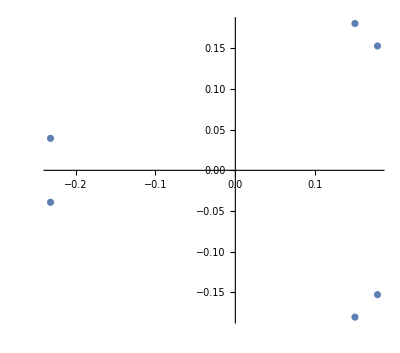

```mathematica
x23//ComplexListPlot
```

```mathematica
x26 = {{0.2637626158259759}, {-0.004824671311807336+0.26371848637154427 ⅈ}, {-0.1318813079129869-0.22842512587392752 ⅈ}, {-0.004824671311777939-0.2637184863715136 ⅈ}, {0.2637626158259759}, {-0.22597457298943685+0.13603753110670416 ⅈ}, {-0.13188130791297595+0.22842512587396205 ⅈ}, {-0.22597457298923063-0.1360375311066803 ⅈ}, {0.26376261582589766}}//Flatten;
```

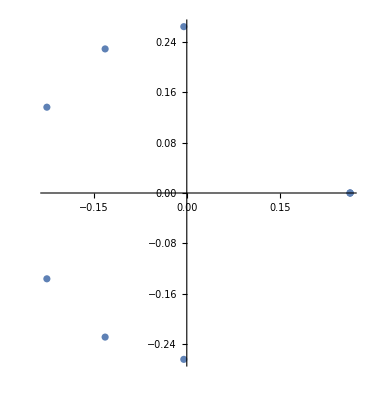

```mathematica
x26//ComplexListPlot
```

Task: write 0.263763` exactly a

```mathematica
0.2087121525221504/0.23462835144947158
```

0.889544

```mathematica
0.23462835144947158/0.26376261582589766
```

0.889544

```mathematica
1/0.8895436175244152
```

1.12417

```mathematica
0.8895436175244152//RootApproximant
```

Root0.890Root[-3+3 #1^2+#1^4&,2]0.8895436175241325

```mathematica
1/Root"0.890"Root[-3+3 #1^2+#1^4&,2]0.8895436175241325//RootApproximant
```

Root1.12Root[-1-3 #1^2+3 #1^4&,2]1.1241719689735967

```mathematica
(* scaling factor between moduli: *) Sqrt[1/2 +1/6 √21]//FullSimplify
```

√(1/6 (3+√21))

```mathematica
1/(Quantum[7,q]-1)//N//Chop
```

0.207874

It seems like we’ve pinned down the moduli of these sets of complex numbers. Now we just need to figure out what the arguments mean

```mathematica
360(x23//Arg)/(2Pi)
```

{-50.3494,40.6987,-170.349,50.3494,-40.6987,170.349}

```mathematica
40.69873111805558+50.349365559028+170.34936555903184
```

261.397

```mathematica
(2Pi)261.3974622361154/360
```

4.56225

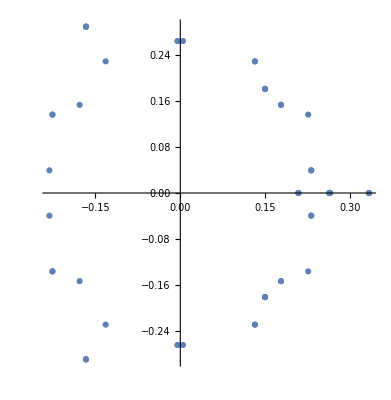

```mathematica
Join[numericalPg[[1;;9]],numericalPg[[78;;93]],numericalPg[[103;;118]],numericalPg[[176;;191]]]//ComplexListPlot
```